```mathematica
Eigenvalues[Table[{x[i]},{i,1,5}].{Table[x[i],{i,1,5}]}]
```

{0,0,0,0,x[1]^2+x[2]^2+x[3]^2+x[4]^2+x[5]^2}

```mathematica
Eigenvectors[Table[{x[i]},{i,1,5}].{Table[x[i],{i,1,5}]}]
```

{{-x[5]/x[1],0,0,0,1},{-x[4]/x[1],0,0,1,0},{-x[3]/x[1],0,1,0,0},{-x[2]/x[1],1,0,0,0},{x[1]/x[5],x[2]/x[5],x[3]/x[5],x[4]/x[5],1}}

```mathematica
Plus@@Eigenvectors[Table[{x[i]},{i,1,5}].{Table[x[i],{i,1,5}]}]
```

{-x[2]/x[1]-x[3]/x[1]-x[4]/x[1]+x[1]/x[5]-x[5]/x[1],1+x[2]/x[5],1+x[3]/x[5],1+x[4]/x[5],2}

```mathematica
Solve[Thread[Flatten[{{1,0},{1,1}}.{{p11,p12},{p12,p22}}+{{p11,p12},{p12,p22}}.{{1,1},{0,1}}+ρ{{1,1},{1,1}}-{{p11,p12},{p12,p22}}.{{0},{1}}.{{0,1}}.{{p11,p12},{p12,p22}}]==0],{p11,p12,p22}]
```

{{p11→0,p22→2-√ρ,p12→-√ρ},{p11→0,p22→2+√ρ,p12→√ρ},{p11→2 (2-√(4+ρ)),p22→(2 ρ-ρ √(4+ρ))/ρ,p12→2-√(4+ρ)},{p11→2 (2+√(4+ρ)),p22→(2 ρ+ρ √(4+ρ))/ρ,p12→2+√(4+ρ)}}

```mathematica
Solve[Thread[Flatten[{{1,1},{0,1}}.{{p11,p12},{p12,p22}}+{{p11,p12},{p12,p22}}.{{1,0},{1,1}}+{{1,1},{1,1}}-σ^-1{{p11,p12},{p12,p22}}.{{1},{0}}.{{1,0}}.{{p11,p12},{p12,p22}}]==0],{p11,p12,p22}]
```

{{p22→0,p11→-√σ+2 σ,p12→-√σ},{p22→0,p11→√σ+2 σ,p12→√σ},{p22→2 (2 σ-√(σ (1+4 σ))),p11→2 σ-√(σ (1+4 σ)),p12→2 σ-√(σ+4 σ^2)},{p22→2 (2 σ+√(σ (1+4 σ))),p11→2 σ+√(σ (1+4 σ)),p12→2 σ+√(σ+4 σ^2)}}

```mathematica
Expand[-2+√ρ+((2-√ρ)^2-ρ)/2]
```

-√ρ

```mathematica
Expand[-2-√(4+ρ)+((2+√(4+ρ))^2-ρ)/2]
```

2+√(4+ρ)

```mathematica
Expand[(p22-2+√ρ)(p22-2-√ρ)]
```

4-4 p22+p22^2-ρ

```mathematica
Expand[(p22-2 -√(4+ρ))(p22-2 + √(4+ρ))]
```

-4 p22+p22^2-ρ

```mathematica
CoefficientList[Expand[(-4 p22+p22^2-ρ)(4-4 p22+p22^2-ρ)],p22]
```

{-4 ρ+ρ^2,-16+8 ρ,20-2 ρ,-8,1}

```mathematica
Eigenvalues[{{p11,p12},{p12,p22}}/.{p11->0,p22->2+√ρ,p12->+√ρ}]
```

{1/2 (2+√ρ-√(4+4 √ρ+5 ρ)),1/2 (2+√ρ+√(4+4 √ρ+5 ρ))}

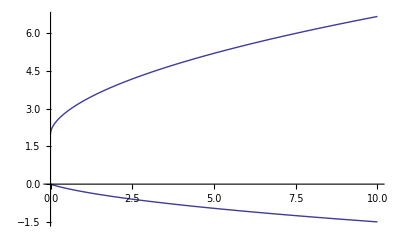

```mathematica
Plot[Eigenvalues[{{p11,p12},{p12,p22}}/.{p11->0,p22->2+√ρ,p12->+√ρ}],{ρ,0,10}]
```

```mathematica
Eigenvalues[{{p11,p12},{p12,p22}}/.{p11->2 (2+√(4+ρ)),p22->2+√(4+ρ),p12->2+√(4+ρ)}]
```

{1/2 (6+3 √(4+ρ)-√(4-4 ρ+20 √(4+ρ)+9 (4+ρ))),1/2 (6+3 √(4+ρ)+√(4-4 ρ+20 √(4+ρ)+9 (4+ρ)))}

```mathematica
FullSimplify[4-4 ρ+20 √(4+ρ)+9 (4+ρ)]
```

5 (8+ρ+4 √(4+ρ))

```mathematica
Eigenvalues[{{1,1},{0,1}}+{{0},{m}}.{{1,1}}(2+√(4+ρ))]
```

{1/2 (2+2 m+m √(4+ρ)-√(-4+(-2-2 m-m √(4+ρ))^2)),1/2 (2+2 m+m √(4+ρ)+√(-4+(-2-2 m-m √(4+ρ))^2))}

```mathematica
Eigenvalues[{{1,1},{0,1}}-{{0},{m}}.{{1,1}}(2+√(4+ρ))]/.{m->1,ρ->5}
```

{1/2 (-3-√5),1/2 (-3+√5)}

```mathematica
Reduce[2+2 m+m √(4+ρ)<0,m,Reals]
```

(-4≤ρ<0&&m<4/ρ+2 √((4+ρ)/ρ^2))||(ρ==0&&m<-1/2)||(ρ>0&&m<4/ρ-2 √((4+ρ)/ρ^2))

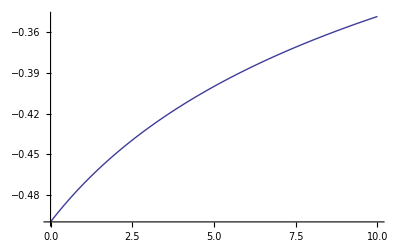

```mathematica
Plot[4/ρ-2 √((4+ρ)/ρ^2),{ρ,0,10}]
```

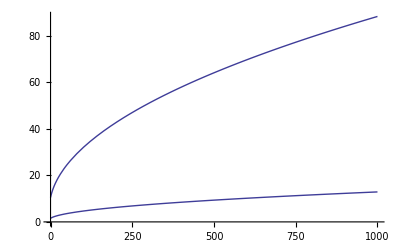

```mathematica
Plot[Eigenvalues[{{p11,p12},{p12,p22}}/.{p11->2 (2+√(4+ρ)),p22->2+√(4+ρ),p12->2+√(4+ρ)}],{ρ,0,1000}]
```